```mathematica
Clear["Global`*"]
```

## Output the data

```mathematica
MI[φ_,NN_]:=1-1/(2 Log[2])-Cos[φ/2]^(4NN)/(2(1-Cos[φ/2]^(2NN)))Log[2,Cos[φ/2]^(2NN)]-(1+Cos[φ/2]^(2NN))/2 Log[2,1+Cos[φ/2]^(2NN)];
F[φ_,NN_]:=2/3+1/3 Cos[φ/2]^NN Cos[(NN φ)/2];
IF[φ_,NN_]:=1/2(1+Cos[φ/2]^(2NN))(1-8/9((1+Cos[φ/2]^NN+Cos[φ/2]^(2NN))^2)/((1+Cos[φ/2]^NN)^2(1+Cos[φ/2]^(2NN))))+1/2(1-Cos[φ/2]^(2NN))(1-π^2/64);
```

```mathematica
qubitIFN=ParallelTable[
{NN,
MI[π/32.,NN],
IF[π/32.,NN],
F[π/32.,NN]},
{NN,1,4000}];
```

```mathematica
Export["Qubit_IF2_NN.dat",SetAccuracy[qubitIFN,6],"Table"]
```

Qubit_IF2_NN.dat

```mathematica
qubitIFN1=ParallelTable[
{φ,
MI[φ,1],
IF[φ,1],
F[φ,1]},
{φ,0.02,6.14,0.02}];
```

```mathematica
Export["Qubit_IF2_N1.dat",SetAccuracy[qubitIFN1,6],"Table"]
```

Qubit_IF2_N1.dat

### Single Measurement

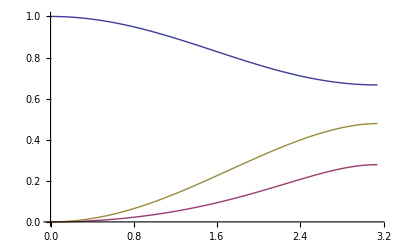

```mathematica
Plot[{F[φ,1],MI[φ,1],IF[φ,1]},{φ,0,π}]
```

### N Measurements

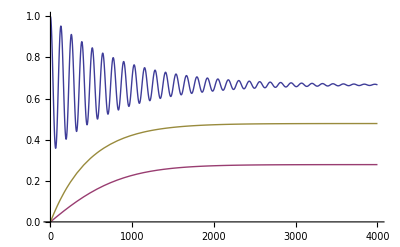

```mathematica
Plot[{F[π/32,NN],MI[π/32,NN],IF[π/32,NN]},{NN,1,4000}]
```

```mathematica
1.-4/9-π^2/128
```

0.478449

```mathematica
1-1./(2Log[2])
```

0.278652

```mathematica
Log[E]
```

1